```mathematica
image=Import["/Users/rhariadi/Downloads/1000stacks-400px.tif","ImageList"];
```

```mathematica
ImageAdjust[image⟦1⟧]
```

-Graphics-

```mathematica
xy={112.125,307.19140624999994}(*{267.25,246.50000000000003}*)(*{121.3046875,72.06250000000006}*);
xy=Round[xy];
```

```mathematica
imageCropped=Table[ImageTrim[image⟦i⟧,{Round[xy]-{10,10},Round[xy]+{10,10}}],{i,Length[image]}];
```

```mathematica
Manipulate[ImageAdjust[imageCropped⟦i⟧],{i,1,1000,1}]
```

```mathematica
dataFit=ImageData[imageCropped⟦10⟧];
Dimensions[dataFit];
dataFit=Table[{i,j,dataFit⟦i,j⟧},{i,22},{j,22}];
dataFit=Flatten[dataFit,1];
fit2D=NonlinearModelFit[dataFit,{b+a ⅇ^(-((x-x0)^2+(x-y0)^2)/(2 σ^2)),1<x0<Dimensions[dataFit]⟦1⟧,1<y0<Dimensions[dataFit]⟦2⟧,0<σ<(Dimensions[dataFit]⟦1⟧)/5},{{x0,11},{y0,11},{σ,2},a,b},{x,y}];
x2D=fit2D["BestFitParameters"]⟦1,2⟧ 117(*nm/pixel*);
y2D=fit2D["BestFitParameters"]⟦2,2⟧ 117(*nm/pixel*);
```

```mathematica
x2D={};
y2D={};
xy2D={};
For[i=1,i<1000,i++,
{
dataFit=ImageData[imageCropped⟦i⟧];
Dimensions[dataFit];
dataFit=Table[{i,j,dataFit⟦i,j⟧},{i,22},{j,22}];
dataFit=Flatten[dataFit,1];
fit2D=NonlinearModelFit[dataFit,{b+a ⅇ^(-((x-x0)^2+(x-y0)^2)/(2 σ^2)),0<x0<22,0<y0<22,2<σ<5,a>0,b>0},{{x0,14},{y0,14},{σ,3},a,b},{x,y}];
x2Dtemp=fit2D["BestFitParameters"]⟦1,2⟧;
y2Dtemp=fit2D["BestFitParameters"]⟦2,2⟧;
xy2D=Append[xy2D,{x2Dtemp,y2Dtemp}];
}
]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

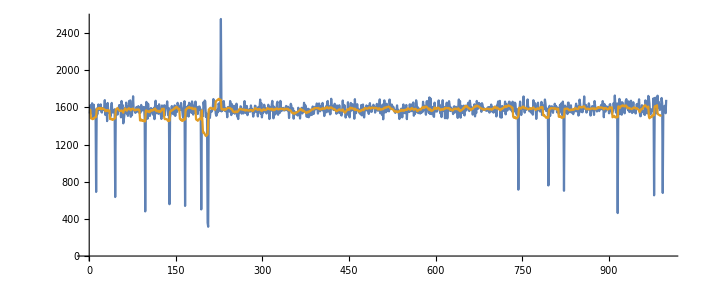

```mathematica
ListLinePlot[{xy2D⟦All,2⟧ 117,MovingAverage[xy2D⟦All,2⟧ 117,10]}(*,PlotRange->{10,22}*),AspectRatio->GoldenRatio/4,PlotRange->All]
```

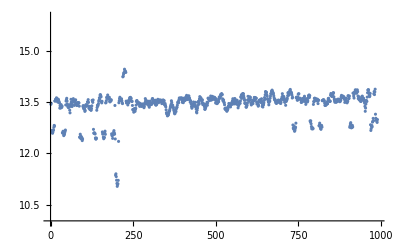

```mathematica
ListPlot[{MovingAverage[xy2D⟦All,2⟧,10]},PlotRange->{10,16}]
```